```mathematica
$Assumptions=Element[theta12,Reals]&&Element[theta13,Reals]&&Element[theta23,Reals]&&Element[delta,Reals];

omega12={{Cos[theta12],Sin[theta12],0},{-Sin[theta12],Cos[theta12],0},{0,0,1}};
omega13={{Cos[theta13],0,Exp[-I*delta]*Sin[theta13]},{0,1,0},{-Exp[I*delta]*Sin[theta13],0,Cos[theta13]}};
omega23={{1,0,0},{0,Cos[theta23],Sin[theta23]},{0,-Sin[theta23],Cos[theta23]}};
omega12//MatrixForm;
omega13//MatrixForm;
omega23//MatrixForm;
u=omega23.omega13.omega12;
energyMatrix={{0,0,0},{0,dm221/(2*energy),0},{0,0,dm231/(2*energy)}};

getProbability[alpha_,beta_,e_,deltaCp_,isNu_]:=Module[{re,im,uuuu,nh,eigenvalues,eigenvectors,um,sign,ve,matterMatrix,h},
sign=If[isNu,1,-1];
ve=sign*Sqrt[2]*gf*ne;
matterMatrix={{ve,0,0},{0,0,0},{0,0,0}};
h=u.energyMatrix.Simplify[ConjugateTranspose[ComplexExpand[u]]]-matterMatrix;

nh=N[h/.values/.energy->e/.delta->deltaCp*sign];
eigenvectors=Eigenvectors[nh];
eigenvalues=Eigenvalues[nh];
um={
{eigenvectors[[1]][[1]],eigenvectors[[2]][[1]],eigenvectors[[3]][[1]]},
{eigenvectors[[1]][[2]],eigenvectors[[2]][[2]],eigenvectors[[3]][[2]]},
{eigenvectors[[1]][[3]],eigenvectors[[2]][[3]],eigenvectors[[3]][[3]]}
};

re=0;
im=0;
For[j=1,j<4,j++,
For[i=j+1,i<4,i++,
uuuu=um[[alpha]][[i]]*Conjugate[um[[beta]][[i]]]*Conjugate[um[[alpha]][[j]]]*um[[beta]][[j]];
re=re+Re[uuuu]*Sin[(eigenvalues[[i]]-eigenvalues[[j]])/2*baseline]^2;
im=im+Im[uuuu]*Sin[(eigenvalues[[i]]-eigenvalues[[j]])*baseline];
]
];
KroneckerDelta[alpha,beta]-4*re+2*im
]

getProbability[2,1,2,3*Pi/2,True]/.values

$Assumptions=True;
```

0.0157745

```mathematica
(*gf*ne=Sqrt[2]/3500 (*1/km*)*)
ne=2.2*avogadroConstant;(*cm-3*)
gf=1.1663787*10^-5;(*GeV-2*)
1/(gf*oneOverGevToCm^2*ne/cmToKm/Sqrt[2])
Clear[gf,ne];
```

2358.14

```mathematica
avogadroConstant=6.02214086*10^23;
oneOverGevToCm=0.197*10^-13;(*cm*)
cmToKm=10^-5;
evToGeV=10^-9;
values={
ne->2.2*avogadroConstant*oneOverGevToCm^3,(*GeV^3*)
gf->1.1663787*10^-5,(*GeV^-2*)
dm221->7.56*10^-5*evToGeV^2,(*GeV^2*)
dm231->2.55*10^-3*evToGeV^2,(*GeV^2*)
baseline->810*10^5/oneOverGevToCm,(*GeV^-1*)
theta13->8.41*Degree,
theta12->34.5*Degree,
theta23->41.*Degree
(*delta->252.*Degree*)
};
```

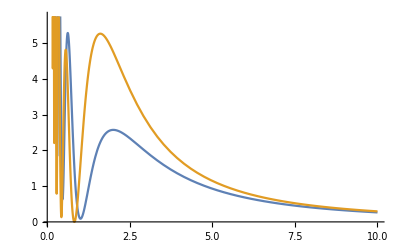

```mathematica
Plot[{getProbability[2,1,x,0,True]*100/.values,
getProbability[2,1,x,0,False]*100/.values},
{x,0.1,10}
]
```

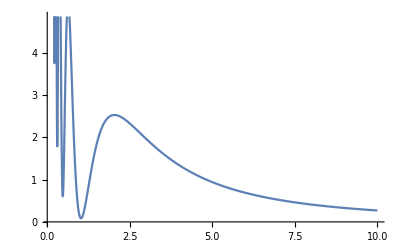

```mathematica
a=gf*ne/Sqrt[2];
getAppearanceProbability[e_,deltaCp_,isNu_]=Module[{sign,a,d21,d31,prob},
sign=If[isNu,1,-1];
a=gf*ne/Sqrt[2]*(-sign);
d21=dm221/(4*e)*baseline;
d31=dm231/(4*e)*baseline;

prob=Sin[theta23]^2*Sin[2*theta13]^2*Sin[d31-a*baseline]^2/(d31-a*baseline)^2*d31^2;
prob=prob+Cos[theta23]^2*Sin[2*theta12]^2*Sin[a*baseline]^2/(a*baseline)^2*d21^2;
prob=prob+Sin[2*theta23]*Sin[2*theta13]*Sin[2*theta12]*Sin[d31-a*baseline]/(d31-a*baseline)*d31*Sin[a*baseline]/(a*baseline)*d21*Cos[d31+delta];
prob/.values/.delta->deltaCp*sign
];
getAppearanceProbability[2,3*Pi/2,False];
Plot[{getAppearanceProbability[x,0,True]*100},
{x,0.1,10}
]
```

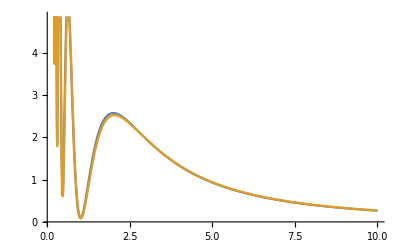

```mathematica
Plot[{getProbability[2,1,x,0,True]*100/.values,
getAppearanceProbability[x,0,True]*100
},
{x,0.1,10}
]
```